```mathematica
TensorData = ToExpression[Import["C:\\ETH\\Neuro\\GlobalTracking\\GlobalTrackingScripts\\tensor_data.txt"]];
dim=Dimensions[TensorData]
Tensor[i_,j_,k_]:={{TensorData[[i,j,k,1]],TensorData[[i,j,k,2]],TensorData[[i,j,k,3]]},{TensorData[[i,j,k,2]],TensorData[[i,j,k,4]],TensorData[[i,j,k,5]]},{TensorData[[i,j,k,3]],TensorData[[i,j,k,5]],TensorData[[i,j,k,6]]}}
```

{9,9,9,6}

```mathematica
g[{ϕ_,θ_}]:={Sin[θ]Cos[ϕ],Sin[θ]Sin[ϕ],Cos[θ]}
angle[vec_]:={   Sign[vec[[2]]]ArcCos[vec[[1]]/Norm[{vec[[1]],vec[[2]]}]]   ,   ArcCos[vec[[3]] ]   }

SurfacePositions = Select[ Flatten[Table[{i,j,k},{i,1,dim[[1]]},{j,1,dim[[2]]},{k,1,dim[[3]]}],2], (#[[1]]==1 ||#[[1]]==dim[[1]] ||#[[2]]==1 ||#[[2]]==dim[[2]]||#[[3]]==1 ||#[[3]]==dim[[3]] )&];
```

### Initialization

```mathematica
Initialize[E0init_,αmaxinit_]:={

αmax = αmaxinit;
E0 =E0init;

Surface = Select[ Flatten[Table[{i,j,k,1},{i,1,dim[[1]]},{j,1,dim[[2]]},{k,1,dim[[3]]}],2], (#[[1]]==1 ||#[[1]]==dim[[1]] ||#[[2]]==1 ||#[[2]]==dim[[2]]||#[[3]]==1 ||#[[3]]==dim[[3]] )&];

S= Table[Eigenvectors[Tensor[i,j,k]][[1]],{i,1,dim[[1]]},{j,1,dim[[2]]},{k,1,dim[[3]]}];
(*S=Table[g[{RandomReal[{0,2Pi}],RandomReal[{0,Pi}]}],{i,1,dim[[1]]},{j,1,dim[[2]]},{k,1,dim[[3]]}];*)

A=Association[
Flatten[
Table[{i,j,k,1}->Association[{
"tensor"->Tensor[i,j,k],
"direction"->S[[i,j,k]],
"position" -> {i,j,k},
"neighbors"-> DeleteCases[
Flatten[
Table[{ii,jj,kk,1},
{ii,Max[1,i-1],Min[dim[[1]],i+1]},{jj,Max[1,j-1],Min[dim[[2]],j+1]},{kk,Max[1,k-1],Min[dim[[3]],k+1]}],
2],
{i,j,k,1}],
"forward"->{},
"backward"->{}}],
{i,1,dim[[1]]},{j,1,dim[[2]]},{k,1,dim[[3]]}],3]
];

AppendTo[A,
{}->Association[{
"tensor"->{},
"direction"->{},
"position" -> {},
"neighbors"-> {},
"forward"->{},
"backward"->{}}]
];
}
```

### Neighborhood Functions

```mathematica
F[spin_]:=Select[
A[spin]["neighbors"],
( (A[#]["position"]-A[spin]["position"]).A[spin]["direction"]>0  && (A[#]["forward"]=={}||A[#]["backward"]=={}) )&
]

B[spin_]:=Select[
A[spin]["neighbors"],
( (A[#]["position"]-A[spin]["position"]).A[spin]["direction"]<=0  && (A[#]["forward"]=={}||A[#]["backward"]=={}) )&
]
```

### Flip Fiber

```mathematica
Flip[{},dir_]:= Null;

Flip[spin_,dir_]:=Module[{forward,backward},

forward = A[spin]["forward"];
backward = A[spin]["backward"];

If[dir == "forwards",

A[spin]["direction"] *= -1.;
A[spin]["backward"] =  forward;
A[spin]["forward"] = {};
Flip[forward,"forwards"]
,
A[spin]["direction"] *= -1.;
A[spin]["forward"] =  backward;
A[spin]["backward"] = {};
Flip[backward, "backwards"]

]
]
```

### Energy Functions

```mathematica
Eint[{}]:=0

Eint[spin_]:=Module[{COSα = {},backward,forward,connection},

forward = A[spin]["forward"];
backward = A[spin]["backward"];

If[backward≠{},
connection =A[backward]["position"]-A[spin]["position"];
AppendTo[COSα,Abs[connection.A[backward]["direction"]/Norm[connection]]];
AppendTo[COSα,Abs[connection.A[spin]["direction"]/Norm[connection]]];
];
If[forward≠{},
connection =A[forward]["position"]-A[spin]["position"];
AppendTo[COSα, Abs[connection.A[forward]["direction"] /Norm[connection]]];
AppendTo[COSα, Abs[connection.A[spin]["direction"]/Norm[connection] ]];
];

 Sum[If[(cosα-Cos[αmax])/(1-Cos[αmax])>0,-Log[(cosα-Cos[αmax])/(1-Cos[αmax])],∞],{cosα,COSα}]

]


Eint[spin1_,spin2_]:=Module[{COSα = {},backward,forward,connection},

connection =A[spin1]["position"]-A[spin2]["position"];

AppendTo[COSα,Abs[connection.A[spin1]["direction"]/Norm[connection]]];
AppendTo[COSα,Abs[connection.A[spin2]["direction"]/Norm[connection]]];


 Sum[If[(cosα-Cos[αmax])/(1-Cos[αmax])>0,-Log[(cosα-Cos[αmax])/(1-Cos[αmax])],∞],{cosα,COSα}]
]

Edata[spin_]:=Module[{Tinv,norm},

Tinv = Inverse[A[spin]["tensor"]];

norm=2/π^2*(Tinv[[1,1]]+Tinv[[2,2]]+2*Tinv[[3,3]]);

A[spin]["direction"].Tinv.A[spin]["direction"]/norm

]
```

### Create New Spin

```mathematica
CreateNew[str_,spin_]:=Module[{newposition,newforward,newbackward,newID},

If[str == "forward",

newposition = Round[A[spin]["position"]+A[spin]["direction"]];

If[1<=newposition[[1]]≤dim[[1]]&&1<=newposition[[2]]≤dim[[2]]&&1<=newposition[[3]]≤dim[[3]],

newID = Length[Select[A,#["position"]==newposition&]]+1;

AppendTo[A,
Append[newposition,newID]->Association[{
"tensor"->A[Append[newposition,newID-1]]["tensor"],
"direction"->A[spin]["direction"],
"position" -> newposition,
"neighbors"-> A[Append[newposition,newID-1]]["neighbors"],
"forward"->{},
"backward"->spin}]
];

newforward=Append[newposition,newID];
A[spin]["forward"] = newforward;

Table[AppendTo[A[n]["neighbors"],newforward],{n,A[newforward]["neighbors"]}];
If[MemberQ[SurfacePositions,newposition],AppendTo[Surface,newforward]];
,
Null;
]

,(*=======================================================*)

newposition = Round[A[spin]["position"]-A[spin]["direction"]];

If[1<=newposition[[1]]≤dim[[1]]&&1<=newposition[[2]]≤dim[[2]]&&1<=newposition[[3]]≤dim[[3]],

newID = Length[Select[A,#["position"]==newposition&]]+1;

AppendTo[A,
Append[newposition,newID]->Association[{
"tensor"->A[Append[newposition,newID-1]]["tensor"],
"direction"->A[spin]["direction"],
"position" -> newposition,
"neighbors"-> A[Append[newposition,newID-1]]["neighbors"],
"forward"->spin,
"backward"->{}}]
];

newbackward=Append[newposition,newID];
A[spin]["backward"] = newbackward;

Table[AppendTo[A[n]["neighbors"],newbackward],{n,A[newbackward]["neighbors"]}];
If[MemberQ[SurfacePositions,newposition],AppendTo[Surface,newbackward]];
,
Null;
]
]
]
```

### Associate Spin

```mathematica
Associate[spin_]:=Module[{oldforward,oldbackward,forwardneighbors={},backwardneighbors,minforward={},minbackward={},E0,E1,Emin},

If[A[spin]["forward"] == {},

forwardneighbors = F[spin];

If[forwardneighbors == {},

CreateNew["forward",spin];
,

Emin =10^10;
Table[

E0 = Eint[spin,newforward];

If[E0<Emin && 
((A[newforward]["direction"].A[spin]["direction"]>0 && A[newforward]["backward"]=={})||
(A[newforward]["direction"].A[spin]["direction"]<0 && A[newforward]["forward"] == {})),
Emin = E0;
minforward = newforward;
]
,{newforward,forwardneighbors}];

If[minforward=={},
CreateNew["forward",spin];
,
If[A[minforward]["direction"].A[spin]["direction"]<0 ,
Flip[minforward,"forwards"];
A[spin]["forward"] = minforward;
A[minforward]["backward"] = spin;
,
A[spin]["forward"] = minforward;
A[minforward]["backward"] = spin;
]
]
]
];

(*========================================*)

If[A[spin]["backward"] == {},

backwardneighbors = B[spin];

If[backwardneighbors == {},

CreateNew["backward",spin];
,

Emin =10^10;
Table[

E0 = Eint[spin,newbackward];

If[E0<Emin && 
((A[newbackward]["direction"].A[spin]["direction"]>0 && A[newbackward]["forward"]=={})||
(A[newbackward]["direction"].A[spin]["direction"]<0 && A[newbackward]["backward"] == {})),
Emin = E0;
minbackward = newbackward;
]
,{newbackward,backwardneighbors}];

If[minbackward=={},
CreateNew["backward",spin];
,
If[A[minbackward]["direction"].A[spin]["direction"]<0 ,
Flip[minbackward,"backwards"];
A[spin]["backward"] = minbackward;
A[minbackward]["forward"] = spin;
,
A[spin]["backward"] = minbackward;
A[minbackward]["forward"] = spin;
]
]
]
];
]
```

### Align Spin

```mathematica
Align[spin_]:=Module[{newdirection,olddirection,E0,E1,p},

olddirection=A[spin]["direction"];

newdirection =  olddirection + RandomReal[{-0.05,0.05},3];
newdirection=newdirection/Norm[newdirection];

E0 = Eint[spin] + Edata[spin];

A[spin]["direction"]=newdirection;

E1 = Eint[spin] + Edata[spin];

p = Min[1., Exp[E0-E1]];

If[RandomReal[]>p,
A[spin]["direction"]=olddirection;
]
]
```

### Testing

```mathematica
EINT={};
EDATA={};
Initialize[1.,Pi/4.];
Block[{i,j,k,n,s,N=10},

For[n=1,n≤N,n++,

EINT = Append[EINT,Sum[Sum[Eint[{i,j,k,s}],{s,1,Length[Select[A,#["position"] == {i,j,k}&]]} ],{i,1,dim[[1]]},{j,1,dim[[2]]},{k,1,dim[[3]]}]];
EDATA = Append[EDATA,Sum[Sum[Edata[{i,j,k,s}],{s,1,Length[Select[A,#["position"] == {i,j,k}&]]}],{i,1,dim[[1]]},{j,1,dim[[2]]},{k,1,dim[[3]]}]];

For[i=2,i<dim[[1]],i++,
For[j=2,j<dim[[2]],j++,
For[k=2,k<dim[[3]],k++,
For[s=1,s≤Length[Select[A,#["position"] == {i,j,k}&]],s++,
Associate[{i,j,k,s}];
]]]]

For[i=1,i<=dim[[1]],i++,
For[j=1,j<=dim[[2]],j++,
For[k=1,k<=dim[[3]],k++,
For[s=1,s≤Length[Select[A,#["position"] == {i,j,k}&]],s++,
Align[{i,j,k,s}];
]]]]

Print[{n,Length[A]}];

];
]
```

{1,796}

{2,821}

{3,838}

{4,849}

{5,854}

{6,856}

{7,856}

{8,856}

{9,856}

{10,856}

```mathematica
EintDistr=Flatten[Table[Table[Eint[{i,j,k,s}],{s,1,Length[Select[A,#["position"] == {i,j,k}&]]}],{i,1,dim[[1]]},{j,1,dim[[2]]},{k,1,dim[[3]]}],3];
```

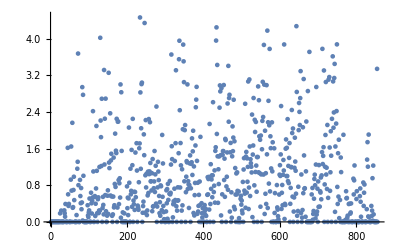

```mathematica
ListPlot[EintDistr]
```

```mathematica
EdataDistr=Flatten[Table[Table[Edata[{i,j,k,s}],{s,1,Length[Select[A,#["position"] == {i,j,k}&]]}],{i,1,dim[[1]]},{j,1,dim[[2]]},{k,1,dim[[3]]}],3];
```

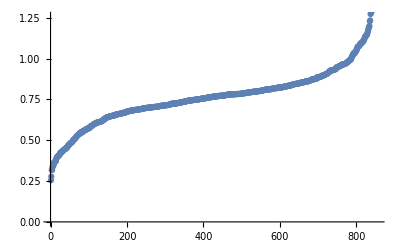

```mathematica
ListPlot[Sort[EdataDistr]]
```

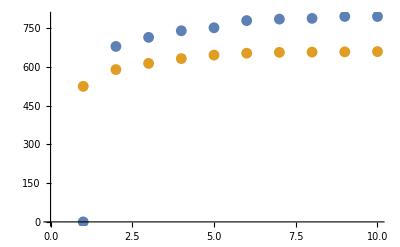

```mathematica
ListPlot[{EINT,EDATA},PlotRange->All]
```